# 基于全球大学生招生数据集的数据可视化实践

## 一、简介

全球大学入学数据集（GLUED）提供了世界各地大学入学数据，系统地整理了大约17000名学生入学数据1950年至2020年间的194个国家和地区的大学。在本数据集中，对大学的定义是提供至少一个学士、硕士或博士课程的机构。本数据集来源于Buckner, Elizabeth. 2022. “Global Longitudinal University Enrollment Dataset (GLUED).” https://doi.org/10.5683/SP3/P0D1KE, Borealis, V1.
文件enrollments.csv 共包含161561行，27列。每一行代表一个大学，每一列的含义如下：
1.国家 2.国家代码 3.地区 4.收入阶层 5.iau代码（用于衡量大学水平） 6.iau代码1（用于曾经合并但后来分离的大学）7.英文名称 8.拉丁语名称 9.成立年份 10.关闭年份 11.是否为私立学校 12.坐标
13.纬度 14.经度 15.是否授予博士学位 16.是否授予硕士学位 17.是否授予本科学位 18.学院数量 19.总学位数量
20.专业数量（total_fields 和 unique_fields两个变量的区别在于它们计算大学提供的学位课程数量的方式不同。total_fields 是指大学在IAU WHED 上列出的所有学位课程的数量，如果一所大学提供了社会学专业的文学士和文学硕士两个学位，那么这两个学位都会被计入 total_fields。而 unique_fields 是指大学在IAU WHED 上列出的独特学位课程的数量，如果一所大学提供了社会学专业的文学士和文学硕士两个学位，那么这两个学位只会被计入 unique_fields 一次。包含这个变量是为了捕捉大学提供的课程广度） 
21.是否为专一型大学  22.是否为合并类大学 23.是否有iau代码  24.年份  25.学生新增人数  26.学生减少人数 27.学生注册人数估计

本次作业主要利用Mathematica软件的可视化功能对以上数据分析，主要包括：

1. 各地区招生大学数量和人口对比
2. 各地区随年份 （1950 - 2020） 招生人数变化 : (1) 时间可视化 (2) 地理可视化 (3) 2020 年录取人数前十的大学
3. 各地区私立学校数变化趋势
4. 各地区收入水平
5. 私立大学与公立大学在其余方面的差异 : (1) 学院数与学位数(2) 本科、硕士、博士招生

## 二、数据处理

导入数据并进行数据清洗

```mathematica
data0=Import["C:\\Users\\zhangyz\\Desktop\\mma大作业\\enrollments.csv","CSV"];
DeleteDuplicates[data0];
```

将其中空缺元素用0填充

```mathematica
data=Map[ToString,data0,{161557}]/. ""->"0";
data=Map[ToExpression,data,{161557}]
```

## 三、各地区招生大学数量和人口对比

data1为各地区大学数量统计，data2为搜集到的各地区人口数（单位：百万人）。绘制成对坐标图，其中左侧为大学数量，右侧为人口数量。

```mathematica
data1={Count[data,{_,_,"East Asia and Pacific",___}],Count[data,{_,_,"Europe and Central Asia",___}],Count[data,{_,_,"Latin America and Caribbean",___}],Count[data,{_,_,"Middle East and North Africa",___}],Count[data,{_,_,"North America",___}],Count[data,{_,_,"South Asia",___}],Count[data,{_,_,"Sub-Saharan Africa",___}]};
data2={49000,920,57000,50000,1877,110000,2000};
PairedBarChart[data1,data2,ChartLegends->{"East Asia and Pacific","Europe and Central Asia","Latin America and Caribbean","Middle East and North Africa","North America","South Asia","Sub-Saharan Africa"},PlotLabel->"各地区大学招生数量和人口对比图" ,ChartStyle->33]
```

-Graphics-

可以看出，东亚和太平洋地区人口数中等，但大学数量较多。欧洲和中亚地区人口数量较少，但大学数量多，位居各地区榜首。北美地区和拉丁美洲和加勒比地区、中东和北非地区、南亚地区人口数多，但大学数都较少，其中南亚地区比例失衡最明显 。通过以上各地区国家数量和学校数量的对比，可以初步推测各地区教育资源质量以及人口的受教育程度。例如，北美、东亚和太平洋地区受教育程度较高，但亚撒哈拉地区、南亚、中东和北非地区教育资源少，受教育程度较低。

了解世界整体情况后，下面对各个大洲的录取情况作具体分析。

## 四、各地区随年份（1950-2020）招生人数变化

## 1.时间可视化

```mathematica
region={"East Asia and Pacific","Europe and Central Asia","Latin America and Caribbean","Middle East and North Africa","North America","South Asia","Sub-Saharan Africa"};
```

```mathematica
time={};yearList={};yearCount={};

time=Table[Select[data,MemberQ[#,region[[i]]]&],{i,Length[region]}];
yearList=Table[time[[i,All,24]],{i,Length[region]}];
yearCount=Table[Tally[yearList[[i]]],{i,Length[region]}];
```

```mathematica
yearCount1=Map[SortBy[#,First]&,yearCount];(*无序数据可能以出乎预料的方式显示，故按年份进行排序*)
```

```mathematica
plots=Table[ListLinePlot[yearCount1[[i]],PlotLabel->region[[i]],Frame->True,FrameLabel->{"Year","Count"}],{i,Length[region]}];
```

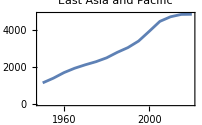
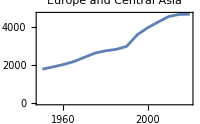
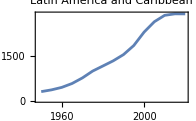
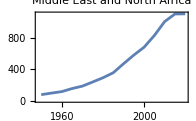
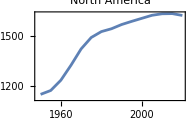
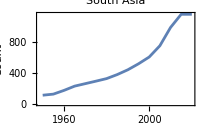
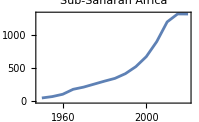

```mathematica
Row[plots,ImageSize->Full]
```

从以上7幅图中可以看出，各地区的大学录取人数均逐年上涨。相较于1950年，各地区大学录取人数均取得了较大飞跃。其中欧洲和中亚地区、拉丁美洲和加勒比地区在2010-2020年间涨幅极快。

## 2.地理可视化

下面进一步通过地理可视化来直观感受1950和2020年各个国家录取人数的情况

```mathematica
data1950=Select[data,IntegerQ[#[[24]]]&&#[[24]]==1950&];
```

统计1950年各个国家大学数量

```mathematica
countryCount=Counts[Transpose[data1950][[1]]];
```

```mathematica
sublist=KeyValueMap[List,countryCount];
```

手动处理部分不规则的国家名称和数据

```mathematica
sublist={{"Afghanistan",3},{"Albania",2},{"Algeria",6},{"Argentina",14},{"Armenia",15},{"Australia",21},{"Austria",26},{"Azerbaijan",17},{"Bangladesh",5},{"Belarus",20},{"Belgium",48},{"Belize",1},{"Bolivia",8},{"BosniaAndHerzegovina",1},{"Brazil",72},{"Bulgaria",27},{"Cambodia",6},{"Canada",73},{"Chile",13},{"China",338},{"Colombia",41},{"Congo",1},{"Costa Rica",3},{"Croatia",1},{"Cuba",6},{"Czech Republic",16},{"Denmark",22},{"DominicanRepublic",2},{"Ecuador",8},{"Egypt",5},{"ElSalvador",1},{"Estonia",5},{"Eswatini",1},{"Ethiopia",2},{"Fiji",2},{"Finland",16},{"France",196},{"Georgia",13},{"Germany",140},{"Ghana",3},{"Greece",14},{"Guatemala",1},{"Haiti",6},{"Holy See",16},{"Honduras",3},{"Hungary",36},{"Iceland",5},{"India",79},{"Indonesia",15},{"Iran",16},{"Iraq",7},{"Ireland",18},{"Israel",17},{"Italy",42},{"Jamaica",3},{"Japan",325},{"Kazakhstan",18},{"Kenya",7},{"Korea",98},{"KyrgyzRepublic",7},{"Latvia",11},{"Lebanon",10},{"Lesotho",1},{"Liberia",2},{"Lithuania",12},{"Luxembourg",1},{"Malawi",1},{"Malaysia",3},{"Mali",1},{"Malta",1},{"Mexico",77},{"Moldova",7},{"Mongolia",4},{"Mrocco",5},{"Myanmar",9},{"Netherlands",22},{"NewZealand",11},{"Nicaragua",4},{"Nigeria",2},{"NorthMacedonia",1},{"Norway",16},{"Pakistan",20},{"Palestine",3},{"Panama",2},{"Paraguay",2},{"Peru",15},{"Philippines",273},{"Poland",81},{"Portugal",11},{"Romania",46},{"Russia",369},{"SaudiArabia",1},{"Senegal",1},{"Serbia",1},{"SierraLeone",1},{"Singapore",3},{"SlovakRepublic",9},{"Slovenia",1},{"SouthAfrica",20},{"Spain",49},{"SriLanka",4},{"Sudan",4},{"Sweden",23},{"Switzerland",14},{"SyrianArabRepublic",3},{"Tajikistan",8},{"Thailand",36},{"TrinidadAndTobago",2},{"Tunisia",1},{"Turkey",18},{"Turkmenistan",5},{"Uganda",2},{"Ukraine",154},{"UnitedKingdom",192},{"UnitedStates",1079},{"Uruguay",4},{"Uzbekistan",24},{"Venezuela",10},{"Vietnam",13},{"Zimbabwe",1}};
```

```mathematica
geoValues=Rule@@@({Entity["Country",#[[1]]],#[[2]]}&/@sublist);

GeoRegionValuePlot[geoValues,GeoRange->"World"]
```

-Graphics-

统计2020年各个国家大学数量

```mathematica
data2020=Select[data,IntegerQ[#[[24]]]&&#[[24]]==2020&];
```

```mathematica
countryCount1=Counts[Transpose[data2020][[1]]];
```

```mathematica
sublist1=KeyValueMap[List,countryCount1];
```

```mathematica
sublist1={{"Afghanistan",45},{"Albania",28},{"Algeria",97},{"Andorra",2},{"Angola",46},{"Argentina",114},{"Armenia",59},{"Aruba",2},{"Australia",85},{"Austria",64},{"Azerbaijan",45},{"Bahamas",1},{"Bahrain",15},{"Bangladesh",120},{"Barbados",1},{"Belarus",50},{"Belgium",103},{"Belize",5},{"Benin",32},{"Bhutan",3},{"Bolivia",51},{"BosniaAndHerzegovina",39},{"Botswana",13},{"Brazil",919},{"BruneiDarussalam",4},{"Bulgaria",62},{"BurkinaFaso",46},{"Burundi",6},{"CaboVerde",8},{"Cambodia",45},{"Cameroon",42},{"Canada",155},{"CentralAfricanRepublic",4},{"Chad",10},{"Chile",71},{"China",1197},,{"Colombia",244},{"Comoros",1},{"Congo",55},{"CostaRica",54},{"CôteD'Ivoire",97},{"Croatia",37},{"Cuba",53},{"Curaçao",1},{"Cyprus",32},{"czech republic",46},{"denmark",46},{"Djibouti",1},{"DominicanRepublic",37},{"Ecuador",60},{"Egypt",55},{"ElSalvador",30},{"EquatorialGuinea",1},{"Eritrea",7},{"Estonia",11},{"Eswatini",4},{"Ethiopia",66},{"FaroeIslands",1},{"Fiji",7},{"Finland",56},{"france",440},{"Gabon",17},{"Georgia",49},{"Germany",383},{"Ghana",77},{"Greece",37},{"Grenada",2},{"Guatemala",38},{"Guinea",39},{"GuineaBissau",7},{"Guyana",4},{"Haiti",17},{"HolySee",21},{"Honduras",18},{"Hungary",58},{"Iceland",10},{"India",813},{"Indonesia",965},{"Iran",237},{"Iraq",103},{"Ireland",52},{"Israel",60},{"Italy",103},{"Jamaica",8},{"Japan",804},{"Jordan",31},{"Kazakhstan",113},{"Kenya",51},{"KoreaRepublicOf",326},{"Kuwait",11},{"KyrgyzRepublic",28},{"LaoPeople'sDemocraticRepublic",7},{"Latvia",26},{"lebanon",41},{"Lesotho",2},{"Liberia",6},{"Libya",14},{"Liechtenstein",3},{"Lithuania",22},{"Luxembourg",1},{"Madagascar",49},{"Malawi",19},{"Malaysia",82},{"Maldives",7},{"Mali",8},{"Malta",3},{"Mauritania",4},{"Mauritius",7},{"Mexico",776},{"Moldova",24},{"Monaco",2},{"Mongolia",52},{"Montenegro",8},{"Morocco",157},{"Mozambique",40},{"Myanmar",80},{"Namibia",4},{"Nepal",11},{"Netherlands",77},{"NewZealand",30},{"Nicaragua",52},{"Niger",11},{"Nigeria",128},{"NorthMacedonia",18},{"Norway",53},{"Oman",53},{"Pakistan",128},{"Palestine",29},{"Panama",26},{"PapuaNewGuinea",6},{"Paraguay",66},{"Peru",145},{"Philippines",944},{"Poland",368},{"Portugal",95},{"Qatar",4},{"Romania",90},{"RussianFederation",754},{"Rwanda",19},{"SaintKittsAndNevis",1},{"Samoa",2},{"SanMarino",1},{"SaoTomeAndPrincipe",1},{"SaudiArabia",72},{"Senegal",68},{"Serbia",15},{"Seychelles",1},{"SierraLeone",4},{"Singapore",11},{"SlovakRepublic",34},{"Slovenia",42},{"SolomonIslands",2},{"Somalia",40},{"SouthAfrica",59},{"SouthSudan",5},{"Spain",137},{"SriLanka",26},{"Sudan",78},{"Suriname",2},{"Sweden",62},{"Switzerland",34},{"SyrianArabRepublic",20},{"Tajikistan",20},{"Tanzania",35},{"Thailand",145},{"Gambia",1},{"TimorLeste",1},{"Togo",19},{"Tonga",1},{"TrinidadAndTobago",6},{"Tunisia",42},{"Turkey",193},{"Turkmenistan",16},{"Uganda",40},{"Ukraine",304},{"UnitedArabEmirates",52},{"UnitedKingdom",265},{"UnitedStates",1466},{"Uruguay",16},{"Uzbekistan",63},{"Venezuela",82},{"Vietnam",173},{"Yemen",12},{"Zambia",29},{"Zimbabwe",13}};
```

```mathematica
geoValues1=Rule@@@({Entity["Country",#[[1]]],#[[2]]}&/@sublist1);
GeoRegionValuePlot[geoValues1,GeoRange->"World"]
```

-Graphics-

## 3、2020年录取人数前十的大学

```mathematica
sortedList=SortBy[data2020,-#[[27]]&];
```

```mathematica
top10=Take[sortedList,10];
```

```mathematica
top10=top10[[All,{7,27}]];
```

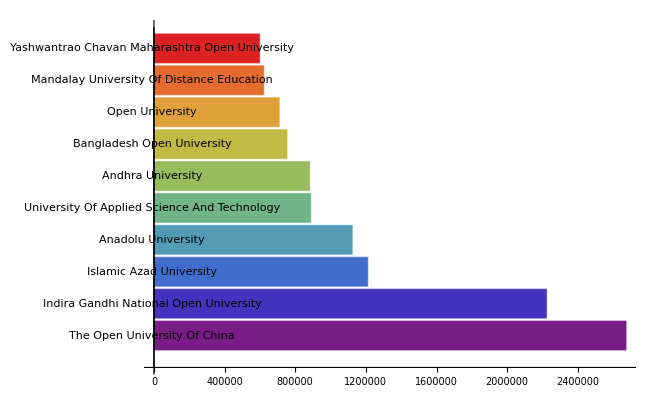

```mathematica
BarChart[top10[[All,2]],ChartLabels->top10[[All,1]],BarOrigin->Left,AxesOrigin->{0,0},ChartStyle->"Rainbow"]
```

## 五、各地区私立学校数变化趋势

```mathematica
private=DeleteCases[data,x_/;(x[[11]]==0)];
time1=Table[Select[private,MemberQ[#,region[[i]]]&],{i,Length[region]}];
yearList1=Table[time1[[i,All,24]],{i,Length[region]}];
yearCount2=Table[Tally[yearList1[[i]]],{i,Length[region]}];
```

```mathematica
yearCount3=Map[SortBy[#,First]&,yearCount2];
```

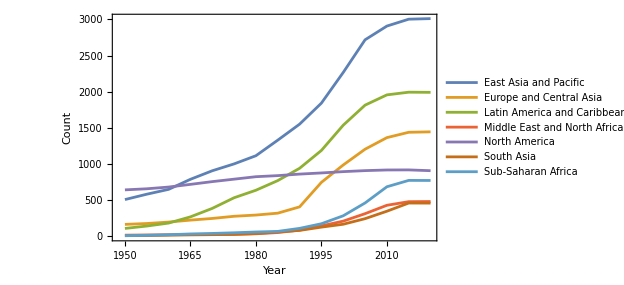

```mathematica
ListLinePlot[yearCount3,PlotLegends->region,Frame->True,FrameLabel->{"Year","Count"}]
```

从上图可以看出，私立学校数量增加是全球化趋势。东亚和太平洋地区、拉丁美洲和加勒比地区、欧洲和中亚涨幅较为明显，中东和北非、南亚地区虽有上升但整体数量仍然较少。此结论与1、2中结论基本相吻合。分析原因，可能是与各地区收入情况有关。下面通过数据中income group进一步分析收入水平。

## 六、各地区收入水平

```mathematica
income=Map[#[[{3,4}]]&,data2020];
```

```mathematica
income1=Table[Select[income,MemberQ[#,region[[i]]]&],{i,Length[region]}];
```

```mathematica
secondElements=Map[#[[All,2]]&,income1];
counts=Counts/@secondElements
```

{<|High income→1205,Lower middle income→1310,Upper middle income→2244,Low income→70|>,<|Upper middle income→1449,High income→2784,Lower middle income→419,Low income→20|>,<|Upper middle income→2609,High income→124,Lower middle income→151,Low income→17|>,<|Lower middle income→381,High income→270,Upper middle income→426,Low income→32|>,<|High income→1621|>,<|Low income→45,Lower middle income→1101,Upper middle income→7|>,<|Lower middle income→640,Upper middle income→94,Low income→577,High income→8|>}

```mathematica
incomecounts={{70,1310,2244,1205},{20,419,1449,2784},{17,151,2609,124},{32,381,426,270},{0,0,0,1621},{45,1101,7,0},{577,640,94,8}};
```

```mathematica
PieChart[incomecounts,ChartLabels->Automatic,ChartLegends->{"Low income","Lower middle income","Upper middle income","High income"},ImageSize->200]
```

-Graphics-

不同环形代表不同地区，从圆心到外分别是East Asia and Pacific , Europe and Central Asia , Latin America and Caribbean, Middle East and North Africa , North America , South Asia , Sub - Saharan Africa

以上内嵌环形图反映了各阶层数量所占比例大小。南亚地区没有高收入阶层，中下阶层密度较大，说明收入情况较差，与私立学校少的结论相符。中东和北非地区、亚撒哈拉地区各阶层分布较为均匀。欧洲和中亚地区、拉丁美洲和加勒比地区中上阶层、高阶层密度较大，说明收入情况较为乐观。北美洲只有高收入阶层，说明该地区经济情况好，可以解释私立学校多、大学录取人数多的结论。
综上，可以看出，各地区收入与大学数量、录取人数、私立大学数量基本呈正相关。

## 七、私立大学与公立大学在其余方面的差异

## 1、学院数与学位数

(1)学院数divisions（对应原始数据的第18列）

```mathematica
department=data[[All,{11,18}]];
department=Drop[department,1];
```

```mathematica
department=DeleteCases[department,{_,"0",___}];(*删去第二个元素为“0”，即原始数据空缺的数据*)
```

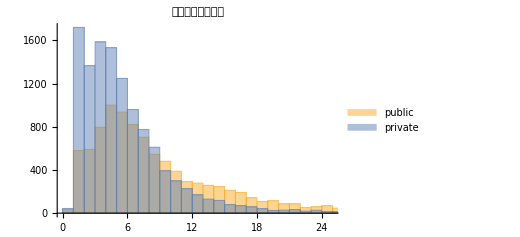

```mathematica
zeros=Select[department,First[#]==0&][[All,2]];
ones=Select[department,First[#]==1&][[All,2]];

Histogram[{zeros,ones},ChartLabels->{"0","1"},ChartLegends->{"public","private"},PlotLabel->HoldForm[学院数直方图对比],LabelStyle->{GrayLevel[0]}]
```

(2)学位数divisions（对应原始数据的第19列）

```mathematica
degree=data[[All,{11,19}]];
degree=Drop[degree,1];
degree=DeleteCases[degree,{_,"0",___}];
```

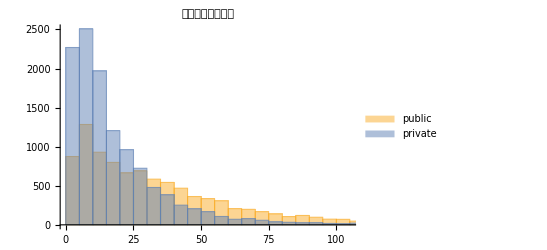

```mathematica
zeros1=Select[degree,First[#]==0&][[All,2]];
ones1=Select[degree,First[#]==1&][[All,2]];

Histogram[{zeros1,ones1},ChartLabels->{"0","1"},ChartLegends->{"public","private"},PlotLabel->HoldForm[学位数直方图对比],LabelStyle->{GrayLevel[0]}]
```

## 2、本科、硕士、博士招生

```mathematica
bachelor=data[[All,{11,17}]];bachelor=Drop[bachelor,1];
master=data[[All,{11,16}]];master=Drop[master,1];
phd=data[[All,{11,15}]];phd=Drop[phd,1];
```

```mathematica
onesb=Select[bachelor,#[[1]]==1&][[All,2]];zerosb=Select[bachelor,#[[1]]==0&][[All,2]];
count00b=Count[zerosb,0];count01b=Count[zerosb,1];count10b=Count[onesb,0];count11b=Count[onesb,1];
```

```mathematica
onesm=Select[master,#[[1]]==1&][[All,2]];zerosm=Select[master,#[[1]]==0&][[All,2]];
count00m=Count[zerosm,0];count01m=Count[zerosm,1];count10m=Count[onesm,0];count11m=Count[onesm,1];
onesp=Select[phd,#[[1]]==1&][[All,2]];zerosp=Select[phd,#[[1]]==0&][[All,2]];
count00p=Count[zerosp,0];count01p=Count[zerosp,1];count10p=Count[onesp,0];count11p=Count[onesp,1];
```

```mathematica
pie1=PieChart[{{count00b,count01b},{count10b,count11b}},ChartLegends->{"no bachelor","bachelor"}];
pie2=PieChart[{{count00m,count01m},{count10m,count11m}},ChartLegends->{"no master","master"}];
pie3=PieChart[{{count00p,count01p},{count10p,count11p}},ChartLegends->{"no phd","phd"}];
```

```mathematica
Grid[{{pie1,pie2,pie3}}]
```

-Graphics- | -Graphics- | -Graphics-

其中内圈为公立学校，外圈为私立学校。从以上三个内嵌环形图可以看出：对于博士学位，公立校和私立校招生的比例均较小，相差不大；对于硕士学位，公立校中招生的学校占比过半，私立校中招生的占比不足一半，远少于公立校；对于本科学位，公立校和私立校招生的比例均较大，公立校略多于私立校。

以上（1）（2）的结论也符合我们通常的认知。公立大学一般拥有比私立大学更大的学生群体。美国学生群体最大的大学就是公立大学，相反，私立学校为保证教育质量，会尽量做到小班授课。这导致了两者在班级规模上有巨大差异。 在教学上，公立大学一般都是人山人海的大班lecture，私立大学则以小班研讨seminar为主。

## 八、总结

本次作业通过对1950-2020年间各国家和地区的大学的入学数据进行数据处理和可视化实践，先从全球角度概览大学数量，然后聚焦于各个地区，通过时间可视化展示了各地区随年份的招生人数变化，通过地理可视化展示了各国家在2020年的招生人数，并统计了2020年录取人数排在前十位的大学。之后着眼于私立学校和公立学校，先展现了私立学校数随时间的变化趋势，然后考虑到可能的影响因素为收入水平，又进行了进一步分析。最后探究了私立大学与公立大学在其余方面的差异。